```mathematica
2-2
```

0

# Physicist's Introduction to Mathematica 6

## Third Edition 2007

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

## Laboratory 3

## Some Useful Standard Packages

The power of Mathematica is greatly enhanced by the large number of Standard Packages that are tucked into its memory, and stand available for activation on an as-needed basis. To find out about those, go to the Documentation Center and search for Standard Packages, which provides links to sources of more specialized information.  The Mathematica Packages provides general information. Standard Package Compatibility Guide opens to reveal a set of eleven topical heads, each of which opens to provide links to a large collection of sites, each of which provides updated information about a specific package.  Many other "non-standard packages" (some proprietary, some not) have been developed to serve specialized needs, and can be discovered on the web: ask Google. Here I can attempt only to illustrate the kind of material that lies hidden away in packages of various descriptions.

### Physical Constants

Go to the Documentation Center and search for PhysicalConstants/tutorial/PhysicalConstants. To install the package, command

```mathematica
Needs["PhysicalConstants`"]
```

You now have at your command such information as the following:

```mathematica
PlanckConstant
```

6.62607×10^-34 Joule Second

```mathematica
SpeedOfLight
```

(299792458 Meter)/Second

```mathematica
EarthRadius
```

6378140 Meter

```mathematica
FineStructureConstant
```

0.00729735

The fine structure constant (e^2/ℏc) is dimensionless (has the same value whatever units are employed), and has approximately the value 1/137:

```mathematica
N[1/137]
```

0.00729927

### Units Conversions

To enable conversion  from one system of units to another on has available the resources of the Units Package. To learn about it, search for Units/tutorial/Units. To activate it, command

```mathematica
Needs["Units`"]
```

This puts you in position to enter such commands as the following:

```mathematica
Convert[95 Calorie, Erg]
```

3.97746×10^9 Erg

```mathematica
Convert[16 Mile,Meter]
```

(3218688 Meter)/125

```mathematica
N[%]
```

25749.5 Meter

```mathematica
Convert[1Year,Second]
```

31536000 Second

How accurate is the claim that "one year is about π 10^7 long"?

```mathematica
31536000/(π 10^7)//N
```

1.00382

```mathematica
Convert[ProtonMass,AtomicMassUnit]
Convert[NeutronMass,AtomicMassUnit]
```

1.00728 AtomicMassUnit

1.00866 AtomicMassUnit

Roughly how many such particles would it take to fabricate the Sun?

```mathematica
Convert[SolarMass,AtomicMassUnit]
```

1.19786×10^57 AtomicMassUnit

```mathematica
MKS[65Mile/Hour]
```

(18161 Meter)/(625 Second)

```mathematica
N[%]
```

(29.0576 Meter)/Second

```mathematica
CGS[65 Mile/Hour]//N
```

(2905.76 Centimeter)/Second

### Calendar

To read about this surprisingly useful "Miscellaneous Standard Package," launch a search for Calendar.  To activate the package, command

```mathematica
Needs["Calendar`"]
```

and I now provide quick illustration of its use. My friend Oya was born on 15 March 1944.

```mathematica
DayOfWeek[{1944,3,15}]
```

Wednesday

we learn that she was born on a Wednesday. I am writing on 31 July 2007, and from

```mathematica
DaysBetween[{1944,3,15},{2007,7,31}]
```

23148

we learn that she is today 23,148 days old. That comes to

```mathematica
Convert[23148 Day,Second]
```

1999987200 Second

so she will—early tomorrow—be able to celebrate a moment when she has become precisely 2 billions seconds old:

```mathematica
Convert[2000000000Second,Day]//N
```

23148.1 Day

## Elementary Algebra

### Short List of Basic Operations

Mathematica has lots to say about algebraic subjects of all descriptions, many quite esoteric. My simple intent here is to discuss the resources that come into view when one goes to Palettes > AlgebraicManipulation, which can be read about by consulting on or another of the eleven tutorial notebooks to which tutorial/AlgebraicManipulationOverview provides links.

Mathematica looks upon (x+y)^7as a primitive object.

```mathematica
(x+y)^7
```

(x+y)^7

But it will expand that binomial if you ask it to:

```mathematica
Expand[(x+y)^7]
Expand[(2+3x+17 x^2)(x^2-9)(x^2+25)]
Expand[(2+3x+17 x^2)(x^2-9)(x^2+25)]//TraditionalForm
```

x^7+7 x^6 y+21 x^5 y^2+35 x^4 y^3+35 x^3 y^4+21 x^2 y^5+7 x y^6+y^7

-450-675 x-3793 x^2+48 x^3+274 x^4+3 x^5+17 x^6

17 x^6+3 x^5+274 x^4+48 x^3-3793 x^2-675 x-450

Standardly, the powers x^n are presented in ascending order.  The command //TraditionalForm reverses the order and adjusts the font.

The action of Together is similarly self-explanatory, and opposite to that of Apart:

```mathematica
Clear[a,b,c,d]
```

```mathematica
Together[a/b+c/d]
```

(b c+a d)/(b d)

```mathematica
Apart[(b c+a d)/(b d)]
```

a/b+c/d

REMARK: It is often more convenient to use post-commands to achieve the same effect:

```mathematica
a/b+c/d//Together
```

(b c+a d)/(b d)

```mathematica
%//Apart
```

a/b+c/d

The Apart command is used to produce the partial fraction representation of ratios, which is often useful in pure/applied mathematical work:

```mathematica
Apart[1/((x-a)(x-b))]
```

1/((a-b) (-a+x))+1/((-a+b) (-b+x))

One uses partial fractions to "separate the singularities," as in the following little example:

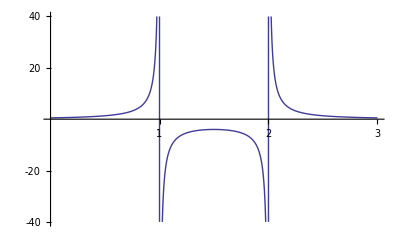

```mathematica
Plot[1/((x-1)(x-2)),{x,0,3},PlotRange->{-40,40}, Ticks->{{1,2,3},{-40,-20,20,40}}]
```

```mathematica
1/((x-1)(x-2))//Apart
```

1/(-2+x)-1/(-1+x)

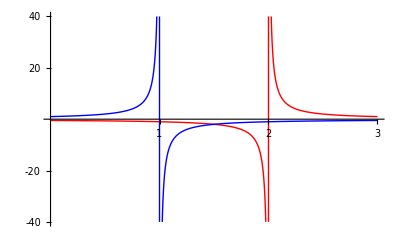

```mathematica
Plot[{1/(-2+x),-1/(-1+x)},{x,0,3},PlotRange->{-40,40}, Ticks->{{1,2,3},{-40,-20,20,40}},PlotStyle->{Red,Blue}]
```

Three very useful commands are

```mathematica
?Cancel
?ExpandDenominator
?ExpandNumerator
```

Cancel[expr] cancels out common factors in the numerator and denominator of expr.

RowBox[{"ExpandDenominator", "[", StyleBox["expr", "TI"], "]"}] expands out products and powers that appear as denominators in StyleBox["expr", "TI"].

RowBox[{"ExpandNumerator", "[", StyleBox["expr", "TI"], "]"}] expands out products and powers that appear in the numerator of StyleBox["expr", "TI"].

—the use of which I now illustrate:

```mathematica
((1+x)(2+x)(7+x))/((1+x)(3+x)(1+2x+3 x^2))//Cancel
```

((2+x) (7+x))/(3+7 x+11 x^2+3 x^3)

```mathematica
((1+x)(2+x)(7+x))/((1+x)(3+x)(1+2x+3 x^2))//ExpandDenominator
```

((2+x) (7+x))/(3+7 x+11 x^2+3 x^3)

```mathematica
((1+x)(2+x)(7+x))/((1+x)(3+x)(1+2x+3 x^2))//ExpandNumerator
```

(14+9 x+x^2)/((3+x) (1+2 x+3 x^2))

One should not confuse the number-theoretic command

```mathematica
?FactorInteger
```

FactorInteger[n] gives a list of the prime factors of the integer n, together with their exponents. 
FactorInteger[n,k] does partial factorization, pulling out at most k distinct factors.

which works this way

```mathematica
FactorInteger[284]
```

{{2,2},{71,1}}

```mathematica
2^2*71
```

284

…with the command

```mathematica
?Factor
```

Factor[poly] factors a polynomial over the integers. 
Factor[poly,Modulus->p] factors a polynomial modulo a prime p. 
Factor[poly,Extension->{a_1,a_2,…}] factors a polynomial allowing coefficients that are rational combinations of the algebraic numbers a_i.

which possesses several optional variants

```mathematica
Options[Factor]
```

{Extension→None,GaussianIntegers→False,Modulus→0,Trig→False}

and works this way:

```mathematica
Factor[x^2-9]
```

(-3+x) (3+x)

```mathematica
Factor[x^2+9]
Factor[x^2+9, GaussianIntegers->True]
```

9+x^2

(-3 ⅈ+x) (3 ⅈ+x)

But factoring 2+3x+17x^2 leads away from the (Gaussian) integers—amounts to looking for roots of the polynomial:

### Finding the Roots of a Polynomial

The celebrated Fundamental Theorem of Algebra (Gauss) asserts that every polynomial of degree n (coefficients real or complex) possesses n roots (real or complex).  Those can be discovered by means of the following commands:

```mathematica
?Solve
?NSolve
```

Solve[eqns,vars] attempts to solve an equation or set of equations for the variables vars. 
Solve[eqns,vars,elims] attempts to solve the equations for vars, eliminating the variables elims.

RowBox[{"NSolve", "[", RowBox[{RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}], ",", StyleBox["var", "TI"]}], "]"}] gives a list of numerical approximations to the roots of a polynomial equation. 
RowBox[{"NSolve", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["eqn", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["eqn", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["var", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["var", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] solves a system of polynomial equations.

```mathematica
Solve[2+3 x+17 x^2==0,x]
```

{{x→1/34 (-3-ⅈ √127)},{x→1/34 (-3+ⅈ √127)}}

```mathematica
NSolve[2+3 x+17 x^2==0,x]
```

{{x→-0.0882353-0.331454 ⅈ},{x→-0.0882353+0.331454 ⅈ}}

The quadratic formula has been known from dim antiquity

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Given a polynomial of order n, one can without loss of generality always arrange to have the the coefficient of x^n be unity, and the coefficient of x^(n-1) be zero. Assume those adjustments to have been made.  In the 16th Century Jerome Cardan, Niccolo Tartaglia and Ludovico Ferrari carried the problem of solving the cubic and quartic as far as one could without knowledge of complex numbers (the invention of which was stimulated by their success):

```mathematica
Solve[ x^3+b x+c==0,x]
```

{{x→-((2/3)^(1/3) b)/((-9 c+√3 √(4 b^3+27 c^2))^(1/3))+((-9 c+√3 √(4 b^3+27 c^2))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))-((1-ⅈ √3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))-((1+ⅈ √3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
Solve[ x^4+a x^2+b x+c==0,x]
```

{{x→1/2 √(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))-1/2 √(-(4 a)/3-(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))-1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3)-(2 b)/(√(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))))},{x→1/2 √(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/2 √(-(4 a)/3-(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))-1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3)-(2 b)/(√(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))))},{x→-1/2 √(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))-1/2 √(-(4 a)/3-(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))-1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3)+(2 b)/(√(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))))},{x→-1/2 √(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/2 √(-(4 a)/3-(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))-1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3)+(2 b)/(√(-(2 a)/3+(2^(1/3) (a^2+12 c))/(3 (2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+27 b^2-72 a c+√(-4 (a^2+12 c)^3+(2 a^3+27 b^2-72 a c)^2))^(1/3))))}}

All efforts to solve the quintic (which everyone expected to be difficult) failed…for what Galois and Abel showed (early 19th Century) to be this very good reason: solution (in the sense of the preceding formulae) is impossible, except in favorable special cases. Mathematica has this to say in the general case:

```mathematica
Solve[ x^5+w x^3+a x^2+b x+c==0,x]
```

{{x→Root[c+b #1+a #1^2+w #1^3+#1^5&,1]},{x→Root[c+b #1+a #1^2+w #1^3+#1^5&,2]},{x→Root[c+b #1+a #1^2+w #1^3+#1^5&,3]},{x→Root[c+b #1+a #1^2+w #1^3+#1^5&,4]},{x→Root[c+b #1+a #1^2+w #1^3+#1^5&,5]}}

But (approximate) numerical solution is possible in all specific cases:  the preceding command supplies an uninformative result

```mathematica
Solve[x^5+ x^3+2 x^2+3 x+4==0,x]//TableForm
```

x→Root[4+3 #1+2 #1^2+#1^3+#1^5&,1]
x→Root[4+3 #1+2 #1^2+#1^3+#1^5&,2]
x→Root[4+3 #1+2 #1^2+#1^3+#1^5&,3]
x→Root[4+3 #1+2 #1^2+#1^3+#1^5&,4]
x→Root[4+3 #1+2 #1^2+#1^3+#1^5&,5]

but look to its numerical sybling:

```mathematica
NSolve[x^5+ x^3+2 x^2+3 x+4==0,x]//TableForm
```

```mathematica
{{x->-1.1181754240534836}, {x->-0.4326913321786198-1.0949614143362267 ⅈ}, {x->-0.4326913321786198+1.0949614143362267 ⅈ}, {x->0.9917790442053616-1.2637504112999582 ⅈ}, {x->0.9917790442053616+1.2637504112999582 ⅈ}}
```

Here is a more legible version of the same statement:

```mathematica
NSolve[x^5+ x^3+2 x^2+3 x+4==0,x,6]//TableForm
```

x→-1.1182
x→-0.43269-1.095 ⅈ
x→-0.43269+1.095 ⅈ
x→0.99178-1.2638 ⅈ
x→0.99178+1.2638 ⅈ

I introduce now a graphic function, the design of which was adapted from Chapter 36 of Glynn & Gray's Beginner's Guide to Mathematica 4:

```mathematica
RootPlot[poly_,s_]:=ListPlot[Map[{Re[#1],Im[#1]} &,x/.N[Solve[poly==0,x]]], PlotRange->{{-s,s},{-s,s}}, AspectRatio->Automatic,PlotStyle->PointSize[.02],AxesLabel->{"Re","Im"}]
```

REMARK: It is surprising to me that in 1992, in an article entitled "Some elements of Mathematica design" (visit ) Wolfram himself wrote at length about why he had avoided the introduction of such an obviously useful command.

Here poly refers to the polynomial whose roots one wants to display as points on the complex plane, and s sets the scale of the figure (PlotRange). The command works like this:

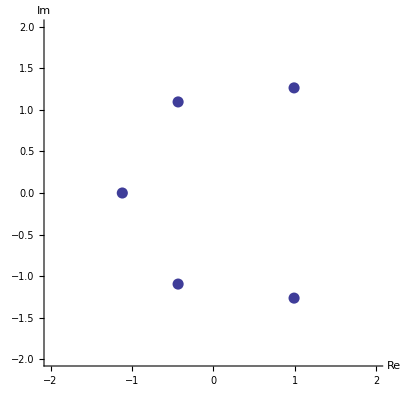

```mathematica
RootPlot[x^5+ x^3+2 x^2+3 x+4,2]
```

#### Another Example

Let

```mathematica
p[x_]:=x^6-2 x^2+4x+4
```

and look to the roots of p[x]=0:

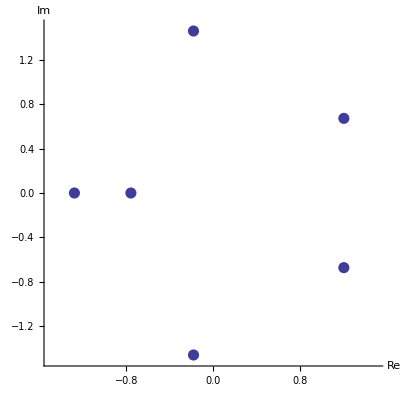

```mathematica
RootPlot[p[x],1.5]
```

When we plot the polynomial

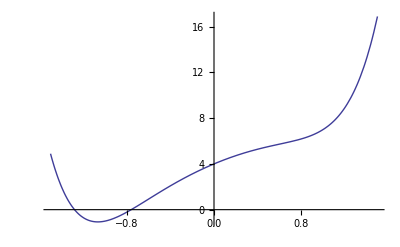

```mathematica
Plot[p[x],{x,-1.5,1.5}]
```

we see the real roots as axis-crossings, but are provided with only an obscure hint concerning the location of the complex roots.

#### Example: The 17th Roots of Unity

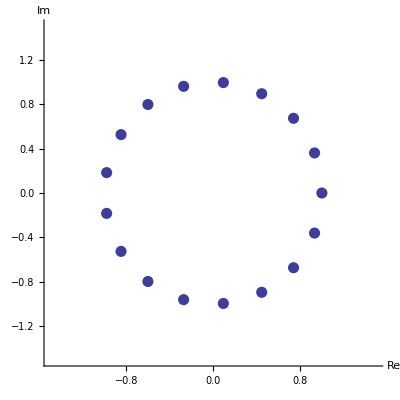

```mathematica
RootPlot[x^17-1,1.5]
```

Quite a similar figure is seen to result from

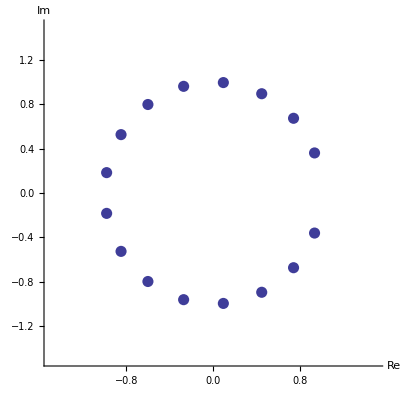

```mathematica
RootPlot[1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12+x^13+x^14+x^15+x^16,1.5]
```

The graphs are so similar because the two polynomials are very closely related:

```mathematica
Series[(x^17-1)/(x-1),{x,0,17}]
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12+x^13+x^14+x^15+x^16+O[x]^18

Removal of the (x-1) factor has erased one of the dots (roots). The remaining 16 roots are the 17th roots of unity except for unity itself:

### Solving Systems of Simultaneous Equations

#### Generic Pair of Inhomogeneous Linear Equations

```mathematica
Clear[a,b,c,d,p,q,x,y]
```

```mathematica
Solve[{a x+b y==p, c x+d y==q},{x,y}]
```

{{x→-(-d p+b q)/(-b c+a d),y→-(-c p+a q)/(b c-a d)}}

Here we ask for an alternative display of the same output:

```mathematica
Solve[{a x+b y==p, c x+d y==q},{x,y}]//TableForm
```

x→-(-d p+b q)/(-b c+a d) | y→-(-c p+a q)/(b c-a d)

#### Triple of Inhomogeneous Linear Equations with Numeric Coefficients

```mathematica
Solve[{1 x+ 2 y+3z==p,4 x+5 y+6z==q,7x+8y+9z==r}, {x,y,r}]//TableForm
```

x→1/3 (-5 p+2 q+3 z) | y→1/3 (4 p-q-6 z) | r→-p+2 q

#### A Nonlinear Coupled Pair

```mathematica
Solve[{x^2+y^2==2,x+y==1},{x,y}]//TableForm
```

x→1/2 (1-√3) | y→1/2 (1+√3)
x→1/2 (1+√3) | y→1/2 (1-√3)

To obtain the numerical evaluation of that result, we might enter the post-command

```mathematica
N[%]
```

{{x→-0.366025,y→1.36603},{x→1.36603,y→-0.366025}}

or might back up and modify the initial command:

```mathematica
NSolve[{x^2+y^2==2,x+y==1},{x,y}]//TableForm
```

x→1.36603 | y→-0.366025
x→-0.366025 | y→1.36603

Here is a graphic representation of what Mathematica has just accomplished:

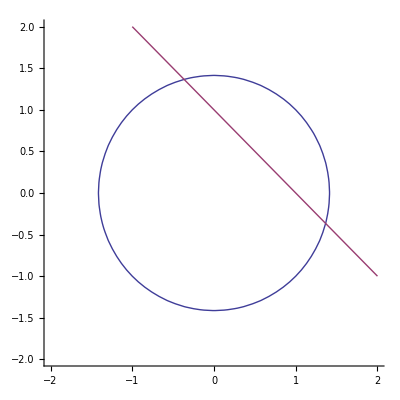

```mathematica
ContourPlot[{x^2+y^2==2,x+y==1},{x,-2,2},{y,-2,2}, Frame->False, Axes->True]
```

#### A Case in which "No Solution Exists"

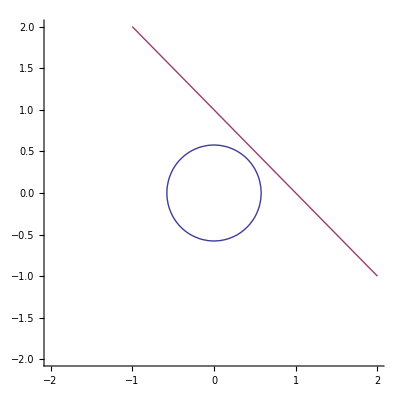

```mathematica
ContourPlot[{x^2+y^2==1/3,x+y==1},{x,-2,2},{y,-2,2}, Frame->False, Axes->True]
```

It is evident to the eye that in this case the curves do not intersect = the system "has no solution." But the command

```mathematica
NSolve[{x^2+y^2==1/3,x+y==1},{x,y}]//TableForm
```

x→0.5-0.288675 ⅈ | y→0.5+0.288675 ⅈ
x→0.5+0.288675 ⅈ | y→0.5-0.288675 ⅈ

reminds us that what we really mean to say is that the system "has no real solution."

#### Application to the Theory of One-dimensional Elastic Collisions

The pre-collisional velocities of M and m are U and u. If the collision is elastic, then both energy and momentum are conserved:  to discover the post-collisional velocities V and v we must solve the coupled system

M V^2+m v^2=M U^2+m u^2

M V+m v=M U+m u

This (on account of the nonlinearity) is a bit tricky when approached analytically, but is duck soup for Mathematica:

```mathematica
Solve[{M V^2+m v^2==M U^2+m u^2, M V+m v==M U+m u}, {V, v}]//TableForm
```

V→U | v→u
V→(2 m u-m U+M U)/(m+M) | v→(m u-M u+2 M U)/(m+M)

The first solution is trivial/spurious, the second describes the effect of a collision, and leads us to define "post-collisional velocity functions"

```mathematica
V[U_,u_,M_,m_]:=(M-m)/(M+m)U+(2m)/(M+m)u
v[U_,u_,M_,m_]:=(2M)/(M+m)U-(M-m)/(M+m)u
```

First illustrtative application: Suppose that M = m and that U = 0.  We then have

```mathematica
List[V[0,u,m,m],v[0,u,m,m]]
```

{u,0}

according to which the identical particles have simply traded velocities.

Second illustrative application: Suppose now that M = 1000 m and that (as before) U = 0. We get

```mathematica
List[V[0,u,1000m,m],v[0,u,1000m,m]]
```

{(2 u)/1001,-(999 u)/1001}

The massive particle (initially at rest) is set into slow motion, while the incident particle rebounds with essentially the negative of its initial velocity.

We look now to an adjustable graphical representation of the algebraic situation.

```mathematica
Manipulate[ContourPlot[{3 x^2+y^2==2w,3x+y==p},{x,-2,2},{y,-2,2}, Frame->False, Axes->True],{{w,1,"energy"},.2,2},{{p,1,"momentum"},-3,3}]
```

It is interesting to note that in cases where line is tangent to ellipse, the point of tangency always occurs on the 45.ba "equi-velocity" line, for this very good reason: if particles are moving with the same velocity then a "collision" is an inconsequential event, a lingering kiss.

If the collision were inelastic then, though the momentum line would remain invariant, the energy ellipse would shrink to tangency, by which time the system would have given up (thermalized) the maximal allowed amount of kinetic energy.

## Trigonometry

Looking again to the AlgebraicManipulation palette, we are reminded that commands like Expand[■], Factor[■] and Simplify[■]are of a type known as formula manipulation commands. We experiment now with some trigonometrically informed relatives of those. The simple commands in question are

```mathematica
?TrigExpand
?TrigFactor
?TrigReduce
?TrigToExp
?ExpToTrig
```

TrigExpand[expr] expands out trigonometric functions in expr.

RowBox[{"TrigFactor", "[", StyleBox["expr", "TI"], "]"}] factors trigonometric functions in StyleBox["expr", "TI"].

RowBox[{"TrigReduce", "[", StyleBox["expr", "TI"], "]"}] rewrites products and powers of trigonometric functions in StyleBox["expr", "TI"] in terms of trigonometric functions with combined arguments.

RowBox[{"TrigToExp", "[", StyleBox["expr", "TI"], "]"}] converts trigonometric functions in StyleBox["expr", "TI"] to exponentials.

RowBox[{"ExpToTrig", "[", StyleBox["expr", "TI"], "]"}] converts exponentials in StyleBox["expr", "TI"] to trigonometric functions.

A few examples will make clear what they do:

```mathematica
TrigExpand[Cos[α+β]]
```

Cos[α] Cos[β]-Sin[α] Sin[β]

```mathematica
TrigFactor[Cos[α]+Cos[β]]
```

2 Cos[α/2-β/2] Cos[α/2+β/2]

```mathematica
TrigExpand[%]
```

Cos[α/2]^2+Cos[β/2]^2-Sin[α/2]^2-Sin[β/2]^2

```mathematica
Simplify[%]
```

Cos[α]+Cos[β]

```mathematica
TrigReduce[Cos[α]^3]
TrigReduce[Cos[α]Sin[β]]
```

1/4 (3 Cos[α]+Cos[3 α])

1/2 (-Sin[α-β]+Sin[α+β])

```mathematica
TrigFactor[%]
```

Cos[α] Sin[β]

```mathematica
TrigToExp[Sin[α]^3]
```

-1/8 ⅈ (ⅇ^(-ⅈ α)-ⅇ^(ⅈ α))^3

```mathematica
ExpToTrig[ⅇ^(ⅈ θ)]
```

Cos[θ]+ⅈ Sin[θ]

```mathematica
Simplify[Sin[α]^2+Cos[α]^2]
```

1

With the aid of the preceding commands one can—with experience—reconstruct and enlarge upon the standard lists of trigonometric identities.  Experience is required because any given trigonometric expression can be written in a zillion ways, and one must learn how to tell Mathematica the goal one has in mind.

And in the latter regard one must be braced for some surprises.  For example: suppose that—with

```mathematica
TrigExpand[(Sin[α]+Sin[β])^2]
```

1-Cos[α]^2/2-Cos[β]^2/2+Sin[α]^2/2+2 Sin[α] Sin[β]+Sin[β]^2/2

in mind—we were to ask for

```mathematica
TrigExpand[(Sin[10 t]+Sin[11 t])^2]
```

1+Cos[t]-Cos[t]^20/2-Cos[t]^21-Cos[t]^22/2+95 Cos[t]^18 Sin[t]^2+210 Cos[t]^19 Sin[t]^2+231/2 Cos[t]^20 Sin[t]^2-4845/2 Cos[t]^16 Sin[t]^4-5985 Cos[t]^17 Sin[t]^4-7315/2 Cos[t]^18 Sin[t]^4+19380 Cos[t]^14 Sin[t]^6+54264 Cos[t]^15 Sin[t]^6+74613/2 Cos[t]^16 Sin[t]^6-62985 Cos[t]^12 Sin[t]^8-203490 Cos[t]^13 Sin[t]^8-159885 Cos[t]^14 Sin[t]^8+92378 Cos[t]^10 Sin[t]^10+352716 Cos[t]^11 Sin[t]^10+323323 Cos[t]^12 Sin[t]^10-62985 Cos[t]^8 Sin[t]^12-293930 Cos[t]^9 Sin[t]^12-323323 Cos[t]^10 Sin[t]^12+19380 Cos[t]^6 Sin[t]^14+116280 Cos[t]^7 Sin[t]^14+159885 Cos[t]^8 Sin[t]^14-4845/2 Cos[t]^4 Sin[t]^16-20349 Cos[t]^5 Sin[t]^16-74613/2 Cos[t]^6 Sin[t]^16+95 Cos[t]^2 Sin[t]^18+1330 Cos[t]^3 Sin[t]^18+7315/2 Cos[t]^4 Sin[t]^18-Sin[t]^20/2-21 Cos[t] Sin[t]^20-231/2 Cos[t]^2 Sin[t]^20+Sin[t]^22/2

This is an unanticipated result.  What's going on?  Mathematica interprets  Sin[10 t] to mean Sin[t+t+t+t+t+t+t+t+t+t] because 10 is an integer.  To get the result we anticipated we must ask Mathematica to think of 10 as just a real number:

```mathematica
TrigExpand[(Sin[10.0 t]+Sin[11.0 t])^2]
```

1-1/2 Cos[10. t]^2-1/2 Cos[11. t]^2+1/2 Sin[10. t]^2+2 Sin[10. t] Sin[11. t]+1/2 Sin[11. t]^2

## Matrices

For introductory information, go to Documentation Center, launch a search for guide/MatrixOperations and examine the TUTORIALS listed at the bottom of the page.  A matrix is a list of lists, so

```mathematica
{{a,b},{c,d}}
{a,b,c,d}
{{a},{b},{c},{d}}
```

{{a,b},{c,d}}

{a,b,c,d}

{{a},{b},{c},{d}}

are all matrices. To produce objects that look more like matrices, enter the commands

```mathematica
MatrixForm[{{a,b},{c,d}}]
{{a,b},{c,d}}//MatrixForm

{{a,b,c,d}}//MatrixForm
{{a},{b},{c},{d}}//MatrixForm
```

(a | b
c | d)

(a | b
c | d)

(a | b | c | d)

(a
b
c
d)

### Creating Matrices

The simplest way to make a matrix appear at the cursor is to proceed Insert > Table/Matrix and select New. [REMARK: In Mathematica 5 one could achieve the same result from the keyboard, by typing ⇧⌘C, but in Mathematica 6 that capability has been lost.] A menu will appear, where you will be asked to state what it is you desire (select amongst several options). Do so, then hit OK. You will have created something like this:

```mathematica
({{□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}})
```

Place the cursor on the 11 box, type a, then type ⇥ b ⇥ c ⇥ d… to produce the following:

```mathematica
Clear[a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p]
```

```mathematica
({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})
```

The column-adding effect of placing the cursor between a and b and typing Ctrl+comma is shown  below

```mathematica
({{a, □, b, c, d}, {e, □, f, g, h}, {i, □, j, k, l}, {m, □, n, o, p}})
```

while the following matrix shows the row-adding effect of placing the cursor as before, but typing Ctrl+⏎

```mathematica
({{a, b, c, d}, {□, □, □, □}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})
```

To remove/modify an element, select that element and hit ⌫; thus

```mathematica
({{a, b, c, d}, {e, f, □, h}, {i, j, k, l}, {m, n, o, p}})
```

To remove a row (or column), select that row/column and hit ⌫; thus

```mathematica
({{a, c, d}, {e, g, h}, {i, k, l}, {m, o, p}})
```

TIP: It rapidly becomes tedious to return again and again to the Table/Matrix menu to create successive matrices of similar structure. In preparing the preceding paragraph, I proceeded in the manner just described to create

(□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □)—actually, to create (a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p)—and then used Copy/Paste.

Notice that options available on the Table/Matrix menu permit one to create matrices with (for example) the structure

```mathematica
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
```

with a single keystroke. Alternatively, one might command

```mathematica
IdentityMatrix[4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

REMARK: When using ⇥ to fill in the elements of  (□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □) it is useful to remember that the control keys ↑, ↓, → and ← act to relocate the "selected box" in obvious ways.

Matrices can constructed at the keyboard, and this is sometimes the fastest way to go. An example serves to describe the simple routing. In Input mode, type ()← to create

```mathematica
()  with the cursor blinking inside
```

Now type aCtrl,bCtrl,cCtrl,d (NOTE: Ctrl, means "type comma with the Ctrl key depressed") to produce

```mathematica
({{a, b, c, d}})  with the cursor blinking after the d
```

Now type Ctrl⏎ to produce

```mathematica
({{a, b, c, d}, {□, □, □, □}})
```

Fill in the new row. How rows can be lengthened/shortened, new rows can be created and old ones elminated should by now be clear.

### Subscripts & Superscripts/Exponents

Subscripts are useful in many contexts, but in matrix algebra they are especially important, since they serve very efficiently  to make it clear who stands where, and to clarify the relatinships that develop. For information, search for tutorial/EnteringTwoDimensionalExpressionsOverview and select Typing Superscripts.

To create

```mathematica
Subscript[a, 1]
```

one might type a and then hit the □_□ button near the bottom of the BasicMathInput palette.  I find it quicker, however, to type aCtrl _1Ctrl⇧, where the final Ctrl⇧ is needed  to get the cursor out of the basement.

Double superscripts are a bit more ticklish. To create

```mathematica
Subscript[a, 12]
```

a_12

you might proceed essentially as before: type aCtrl _12Ctrl⇧. And for many purposes that is sufficient, as I demonstrate:

```mathematica
A=({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}});
B=({{Subscript[b, 11], Subscript[b, 12]}, {Subscript[b, 21], Subscript[b, 22]}});
```

```mathematica
A
B
```

{{a_11,a_12},{a_21,a_22}}

{{b_11,b_12},{b_21,b_22}}

NOTE that Mathematica insists upon thinking of matrices as lists of lists. We look to the matrix product of A and B:

```mathematica
A.B//MatrixForm
```

(a_11 b_11+a_12 b_21 | a_11 b_12+a_12 b_22
a_21 b_11+a_22 b_21 | a_21 b_12+a_22 b_22)

Contexts arise, however, in which one wants Mathematica to think of the subscript on

```mathematica
Subscript[a, 12]
```

a_12

not as a unitary symbol ("twelve" in this instance) but as "one, two". One has then to separate the "one" from the "two" with a comma:

```mathematica
Subscript[a, 1,2]
```

a_(1,2)

If one finds that too distracting in a context like

```mathematica
({{Subscript[a, 1,1], Subscript[a, 1,2]}, {Subscript[a, 2,1], Subscript[a, 2,2]}});
```

```mathematica
%//MatrixForm
```

(a_(1,1) | a_(1,2)
a_(2,1) | a_(2,2))

one can make use of the invisible comma, which is created Esc,Esc. One then has

```mathematica
({{Subscript[a, 1,1], Subscript[a, 1,2]}, {Subscript[a, 2,1], Subscript[a, 2,2]}})//MatrixForm
```

(a_(1,1) | a_(1,2)
a_(2,1) | a_(2,2))

Which looked fine as input, but which as output reacquired its former ugliness.

One might suppose that spaces would do the job, but no:

```mathematica
({{Subscript[a, 1 1], Subscript[a, 1 2]}, {Subscript[a, 2 1], Subscript[a, 2 2]}})//MatrixForm
```

(a_1 | a_2
a_2 | a_4)

Mathematica interprets xy to be a unitary symbol, but x y as a command to construct the product of x and y:

```mathematica
x y===x*y
```

True

IMPORTANT NOTE: In this respect, matrices are exceptional. To signal that matrices A and B are to be multiplied, neither A B  nor A*B works. One must write A.B (as above).

### Superscripts

Identical remarks pertain the creation of superscripted matrices, the only difference being that in place of  aCtrl _12Ctrl⇧ we type pCtrl ^12Ctrl⇧. We have

```mathematica
P=({{p^11, p^12}, {p^21, p^22}});
Q=({{q^11, q^12}, {q^21, q^22}});
```

```mathematica
P
Q
```

{{p^11,p^12},{p^21,p^22}}

{{q^11,q^12},{q^21,q^22}}

```mathematica
P.Q//MatrixForm
```

(p^11 q^11+p^12 q^21 | p^11 q^12+p^12 q^22
p^21 q^11+p^22 q^21 | p^21 q^12+p^22 q^22)

No surprises. But consider:

```mathematica
A.A//MatrixForm
P.P//MatrixForm
```

(a_11^2+a_12 a_21 | a_11 a_12+a_12 a_22
a_11 a_21+a_21 a_22 | a_12 a_21+a_22^2)

(p^22+p^33 | p^23+p^34
p^32+p^43 | p^33+p^44)

Mathematica has interpreted the superscripts to be exponents, and has combined them by the Law of Exponents!!

MORAL: Superscripts are best avoided, not only in matrix algebra but in all algebraic contexts, for they occupy a space reserved for exponents.

### Some Common Matrix Operations

Let the matrix A be defined as before:

```mathematica
A//MatrixForm
```

(a_11 | a_12
a_21 | a_22)

Then to evaluate the trace we command

```mathematica
Tr[A]
```

a_11+a_22

To evaluate the determinant we command

```mathematica
Det[A]
```

-a_12 a_21+a_11 a_22

To construct the transpose we command

```mathematica
Transpose[A]//MatrixForm
```

(a_11 | a_21
a_12 | a_22)

To construct the inverse we command

```mathematica
Inverse[A]
```

{{a_22/(-a_12 a_21+a_11 a_22),-a_12/(-a_12 a_21+a_11 a_22)},{-a_21/(-a_12 a_21+a_11 a_22),a_11/(-a_12 a_21+a_11 a_22)}}

and check that this matrix has the required property:

```mathematica
Inverse[A].A//Simplify//MatrixForm
```

(1 | 0
0 | 1)

Let us now define

```mathematica
rowvector=({{Subscript[a, 1], Subscript[a, 2], Subscript[a, 3]}})
columnvector=({{Subscript[b, 1]}, {Subscript[b, 2]}, {Subscript[b, 3]}})
squarematrix=({{Subscript[m, 11], Subscript[m, 12], Subscript[m, 13]}, {Subscript[m, 21], Subscript[m, 22], Subscript[m, 23]}, {Subscript[m, 31], Subscript[m, 32], Subscript[m, 33]}})
```

{{a_1,a_2,a_3}}

{{b_1},{b_2},{b_3}}

{{m_11,m_12,m_13},{m_21,m_22,m_23},{m_31,m_32,m_33}}

The  following command is only occasionally useful, for it responds to a question that is seldom in doubt:

```mathematica
Dimensions[rowvector]
Dimensions[columnvector]
Dimensions[squarematrix]
```

{1,3}

{3,1}

{3,3}

The matrix product

```mathematica
rowvector.columnvector
```

{{a_1 b_1+a_2 b_2+a_3 b_3}}

```mathematica
%//MatrixForm
```

(a_1 b_1+a_2 b_2+a_3 b_3)

is a 1×1 matrix, a list with a single element, that element being itself a list with a single element, that element being familiar as the dot product. We can use a standard list manipulation technique to peal alway the distracting brackets:

```mathematica
%⟦1⟧
```

{a_1 b_1+a_2 b_2+a_3 b_3}

```mathematica
%⟦1⟧
```

a_1 b_1+a_2 b_2+a_3 b_3

More compactly:

```mathematica
(rowvector.columnvector)⟦1⟧⟦1⟧
```

a_1 b_1+a_2 b_2+a_3 b_3

REMARK: Just about everything, if you penetrate deeply enough into the bowels of Mathematica, becomes a "list" of one sort or another, and elaborate means are provided for the manipulation of lists. Sooner or later you will need to acquire familiarity with some of that material. For basic information, search for tutorial/ListsOverview and look at the links provided there.

Reversing the order of the matrix product studied above, you obtain

```mathematica
columnvector.rowvector//MatrixForm
```

(a_1 b_1 | a_2 b_1 | a_3 b_1
a_1 b_2 | a_2 b_2 | a_3 b_2
a_1 b_3 | a_2 b_3 | a_3 b_3)

which is a 3×3 matrix. Matrices of this specialized design are sometimes called "dyadics."

Here are a couple of matrix operations that—Mathematica is quick to inform you—make no sense:

```mathematica
rowvector.rowvector
columnvector.columnvector
```

Dot::dotsh: Tensors {{a_1, a_2, a_3}} and {{a_1, a_2, a_3}} have incompatible shapes.

{{a_1,a_2,a_3}}.{{a_1,a_2,a_3}}

Dot::dotsh: Tensors {{b_1}, {b_2}, {b_3}} and {{b_1}, {b_2}, {b_3}} have incompatible shapes.

{{b_1},{b_2},{b_3}}.{{b_1},{b_2},{b_3}}

Because matrix multiplication is in some respects a bit quirky, one must take special steps to raise a square matrix to a power. Comparing

```mathematica
({{1, 2}, {3, 4}}).({{1, 2}, {3, 4}})//MatrixForm
```

(7 | 10
15 | 22)

with

```mathematica
({{1, 2}, {3, 4}})^2//MatrixForm
```

(1 | 4
9 | 16)

shows clearly that commands of the latter sort do not do the job (what we have in fact demonstrated is that squaring is a "Listable" operation: the meaning of "Listable" will be discussed in a moment). Available for such purposes is the command

```mathematica
?MatrixPower
```

MatrixPower[m,n] gives the n^th matrix power of the matrix m. 
MatrixPower[m,n,v] gives the n^th matrix power of the matrix m applied to the vector v.

#### Illustrative Application: Rotations in 2-Space

Define

```mathematica
S=({{0, -1}, {1, 0}});
```

Compare

```mathematica
S.S//MatrixForm
MatrixPower[S,2]//MatrixForm
```

(-1 | 0
0 | -1)

(-1 | 0
0 | -1)

Construct

```mathematica
R=∑_(n=0)^6 1/(n!)θ^n MatrixPower[S,n]//MatrixForm
```

(1-θ^2/2+θ^4/24-θ^6/720 | -θ+θ^3/6-θ^5/120
θ-θ^3/6+θ^5/120 | 1-θ^2/2+θ^4/24-θ^6/720)

Pretty clearly, the infinite sum gives

```mathematica
R=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
```

which we recognize to be a rotation matrix:

```mathematica
Simplify[Transpose[R]==Inverse[R]]
```

True

Actually, Mathematica provides a command which eliminates the guesswork, and is very useful in a great variety of pure/applied contexts:

```mathematica
?MatrixExp
```

MatrixExp[m] gives the matrix exponential of m. 
MatrixExp[m,v] gives the matrix exponential of m applied to the vector v.

```mathematica
MatrixExp[θ S]//MatrixForm
```

(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ])

#### Application of a Sort that Arises in Connection with the Solution of Differential Equations

Let

```mathematica
m[t_]:=Exp[a t]
```

Familiarly (if in a not-yet-familiar notation), m'[t] - a m[t] = 0:

```mathematica
m'[t] - a m[t] == 0
```

True

We look to the matrix analog of that elementary result: let

```mathematica
M[t_]:=MatrixExp[({{-1.1, 0.9}, {-1.4, 0.3}})t]
```

This is a fairly complicated matrix-valued function of t:

```mathematica
M[t]
```

{{(0.5-0.398862 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]-ⅈ ⅇ^(-0.4 t) Sin[0.877496 t])+(0.5+0.398862 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]+ⅈ ⅇ^(-0.4 t) Sin[0.877496 t]),(-1.38778×10^-16+0.512823 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]-ⅈ ⅇ^(-0.4 t) Sin[0.877496 t])-(0.+0.512823 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]+ⅈ ⅇ^(-0.4 t) Sin[0.877496 t])},{(0.-0.797724 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]-ⅈ ⅇ^(-0.4 t) Sin[0.877496 t])+(0.+0.797724 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]+ⅈ ⅇ^(-0.4 t) Sin[0.877496 t]),(0.5+0.398862 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]-ⅈ ⅇ^(-0.4 t) Sin[0.877496 t])+(0.5-0.398862 ⅈ) (ⅇ^(-0.4 t) Cos[0.877496 t]+ⅈ ⅇ^(-0.4 t) Sin[0.877496 t])}}

But nevertheless,

```mathematica
M'[t]-({{-1.1, 0.9}, {-1.4, 0.3}}).M[t]//Simplify//Chop//MatrixForm
```

(0 | 0
0 | 0)

where

```mathematica
?Chop
```

Chop[expr] replaces approximate real numbers in expr that are close to zero by the exact integer 0.

has served to remove computational artifacts of the order 10^-17.

### Matrices as Arguments of "Listable" Commands

```mathematica
?Listable
```

Listable is an attribute that can be assigned to a symbol f to indicate that the function f should automatically be threaded over lists that appear as its arguments.

Matrices are lists (of lists), so any command with the attribute "listable" will accept a matrix as its argument: thus

```mathematica
({{1, x}, {x^2, x^3}})+a//MatrixForm
D[({{1, x}, {x^2, x^3}}),x]//MatrixForm
∫({{1, x}, {x^2, x^3}})ⅆx//MatrixForm
```

(1+a | a+x
a+x^2 | a+x^3)

(0 | 1
2 x | 3 x^2)

(x | x^2/2
x^3/3 | x^4/4)

### Characteristic Equation, Eigenvalues, Eigenvectors

I confine my initial illustrative remarks to the 2-dimensional case, and work with the generic matrix

```mathematica
M=({{a, b}, {c, d}});
```

The characteristic polynomial of the matrix is defined

```mathematica
Det[({{a, b}, {c, d}})-λ IdentityMatrix[2]]
```

-b c+a d-a λ-d λ+λ^2

but is achieved  much more simply the following command:

```mathematica
?CharacteristicPolynomial
```

CharacteristicPolynomial[m,x] gives the characteristic polynomial for the matrix m. 
CharacteristicPolynomial[{m,a},x] gives the generalized characteristic polynomial with respect to a.

```mathematica
CharacteristicPolynomial[M,λ]
```

-b c+a d-a λ-d λ+λ^2

The celebrated (and very often valuable) Cayley-Hamilton Theorem asserts—remarkably—that "every matrix satisfies its own characteristic equation." In the present instance we introduce the notations

```mathematica
unitmatrix=IdentityMatrix[2];
nullmatrix=({{0, 0}, {0, 0}});
```

{{1,0},{0,1}}

{{0,0},{0,0}}

and find that we do indeed have the matrix-valued identity

```mathematica
(-b c+a d)unitmatrix-a M-d M+M.M==nullmatrix
```

True

The "eigenvalues" of a square matrix are the roots of its characteristic polynomial. To discover those we might command

```mathematica
Solve[CharacteristicPolynomial[matrix,λ]==0,λ]
```

For the 2×2  M-matrix introduced just above this would give

```mathematica
Solve[CharacteristicPolynomial[M,λ]==0,λ]
```

{{λ→1/2 (a+d-√(a^2+4 b c-2 a d+d^2))},{λ→1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}}

but Mathematica provides a better way:

```mathematica
?Eigenvalues
```

Eigenvalues[m] gives a list of the eigenvalues of the square matrix m. 
Eigenvalues[{m,a}] gives the generalized eigenvalues of m with respect to a. 
Eigenvalues[m,k] gives the first k eigenvalues of m. 
Eigenvalues[{m,a},k] gives the first k generalized eigenvalues.

```mathematica
Eigenvalues[M]//TableForm
```

1/2 (a+d-√(a^2+4 b c-2 a d+d^2))
1/2 (a+d+√(a^2+4 b c-2 a d+d^2))

Thus far we have asked Mathematica to do matrix-theoretic things we could as easily have done by hand. The power of Mathematica is more clearly evident in higher-dimensional situations. To have some representative material to work with, we construct a 5 by 5 matrix with random real-valued elements, making use of the command

```mathematica
?RandomReal
```

RandomReal[] gives a pseudorandom real number in the range 0 to 1. 
RandomReal[{x_min,x_max}] gives a pseudorandom real number in the range x_min to x_max. 
RandomReal[x_max] gives a pseudorandom real number in the range 0 to x_max. 
RandomReal[range,n] gives a list of n pseudorandom reals. 
RandomReal[range,{n_1,n_2,…}] gives an n_1×n_2×…  array of pseudorandom reals. 
RandomReal[dist,…] samples from the symbolic continuous distribution dist.

```mathematica
RandomReal[{-2,2},5]
```

{-1.74104,0.942254,-1.17106,1.41064,-1.44906}

NOTE: In a moment I am going to ask you to return to this point and to repeat the following sequence of commands.

★★★

```mathematica
randomrealmatrix=
{Table[RandomReal[{-2,2}],{5}],
Table[RandomReal[{-2,2}],{5}],
Table[RandomReal[{-2,2}],{5}],
Table[RandomReal[{-2,2}],{5}],
Table[RandomReal[{-2,2}],{5}]};
```

```mathematica
%//MatrixForm
```

(-0.98009 | -1.36423 | 0.196796 | -0.738927 | 0.700561
-1.47151 | -0.759513 | -0.714453 | 0.449598 | -1.77262
0.248506 | 1.57134 | 1.95224 | -1.1965 | 0.234407
1.15014 | -0.117637 | -1.09473 | 1.72798 | -1.1779
-0.0255084 | -0.466377 | 0.233534 | -0.652584 | -0.987185)

To construct the determinant of such a matrix you would have to compute 5! five-number products and add the (appropriately signed) results; observe how quickly Mathematica does the job:

```mathematica
Det[randomrealmatrix]//Timing
```

{0.002822,6.97743}

Next we construct the characteristic polynomial

```mathematica
CharacteristicPolynomial[randomrealmatrix,λ]
```

6.97743-12.0202 λ-7.18935 λ^2+7.17312 λ^3+0.953431 λ^4-λ^5

The some instances, insignificantly small imaginary parts will appear in the coefficients, which are clearly computational artifacts. To get rid of them we would command

```mathematica
Chop[%]
```

6.97743-12.0202 λ-7.18935 λ^2+7.17312 λ^3+0.953431 λ^4-λ^5

Either by computation

```mathematica
Solve[%==0,λ]
```

{{λ→-2.29288},{λ→-1.35506},{λ→0.506963},{λ→2.04721-0.488552 ⅈ},{λ→2.04721+0.488552 ⅈ}}

or by means of the command

```mathematica
Eigenvalues[randomrealmatrix]//TableForm
```

-3.13708
-2.53888
2.29308
0.0132861+1.23941 ⅈ
0.0132861-1.23941 ⅈ

we obtain the eigenvalues of our random 5×5 matrix. Notice that one (or sometimes three, sometimes five) is real, the others occur in conjugate pairs. Reactivating the definition (and making a notational adjustment λ → x as that definition requires)

```mathematica
RootPlot[poly_,s_]:=ListPlot[Map[{Re[#1],Im[#1]} &,x/.N[Solve[poly==0,x]]], PlotRange->{{-s,s},{-s,s}}, AspectRatio->Automatic,PlotStyle->PointSize[.02],AxesLabel->{"Re","Im"}]
```

we construct a graphic description of the spectrum of our 5×5 matrix; i.e., of its population of eigenvalues:

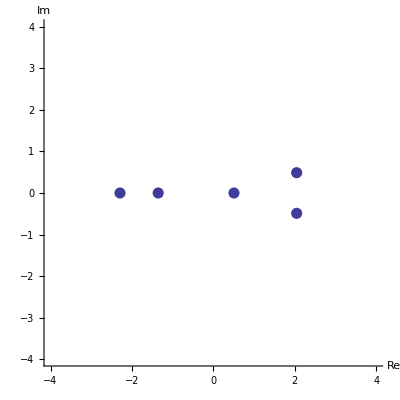

```mathematica
RootPlot[CharacteristicPolynomial[randomrealmatrix,x], 4]
```

Back up now to the point marked ★★★ and repeat that series of commands. Do that several times.  Observe that, while the numbers and final figure change randomly, the qualitative essentials of the situation persist.

Now construct the real symmetric matrix (the "symmetric part" of the current randomrealmatrix)

```mathematica
symmetricpart=1/2(randomrealmatrix+Transpose[randomrealmatrix]);
```

```mathematica
%//MatrixForm
```

(0.140721 | -0.954894 | -0.925611 | -0.627717 | -0.108869
-0.954894 | -1.191 | 0.654076 | 1.36534 | 1.604
-0.925611 | 0.654076 | -1.8187 | 1.35717 | -0.895996
-0.627717 | 1.36534 | 1.35717 | 0.499665 | -1.34916
-0.108869 | 1.604 | -0.895996 | -1.34916 | -0.987002)

The interesting thing about such matrices—revealed by the command

```mathematica
Eigenvalues[symmetricpart]//TableForm
```

3.14828
-2.57809
-1.55063
1.31851
0.615354

is that their eigenvalues are all real:

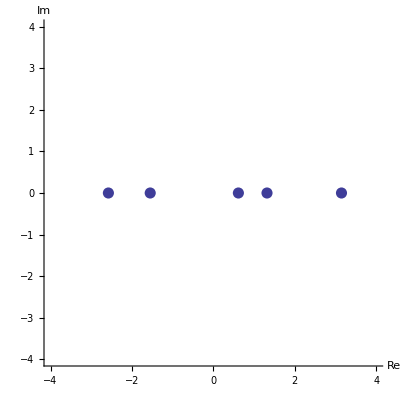

```mathematica
RootPlot[CharacteristicPolynomial[symmetricpart,x], 4]
```

Real numbers that originate in this way—as the eigenvalues of a real symmetric matrix—are of fundamental importance to many branches of physics/engineering and pure/applied mathematics.

Now construct a 5 by 5 matrix with random complex-valued elements

```mathematica
✶✶✶
```

```mathematica
randomcomplexmatrix={
Table[RandomComplex[{-2-2ⅈ,2+2ⅈ}],{5}],
Table[RandomComplex[{-2-2ⅈ,2+2ⅈ}],{5}],Table[RandomComplex[{-2-2ⅈ,2+2ⅈ}],{5}],
Table[RandomComplex[{-2-2ⅈ,2+2ⅈ}],{5}],
Table[RandomComplex[{-2-2ⅈ,2+2ⅈ}],{5}]};
```

Construct also the hermitian part (complex generalization of the real symmetric part) of that matrix:

```mathematica
hermitianpart=1/2(randomcomplexmatrix+Transpose[Conjugate[randomcomplexmatrix]]);
```

```mathematica
%//MatrixForm
```

(-0.327609+0. ⅈ | 0.773733-0.549299 ⅈ | -0.670641+0.871965 ⅈ | 0.937439-0.271433 ⅈ | 0.161895+0.169412 ⅈ
0.773733+0.549299 ⅈ | -0.968069+0. ⅈ | -0.601262+0.433941 ⅈ | 1.31641-0.079024 ⅈ | -1.78377-0.26494 ⅈ
-0.670641-0.871965 ⅈ | -0.601262-0.433941 ⅈ | 1.90723+0. ⅈ | -0.586192-0.0167452 ⅈ | -0.44196-0.254481 ⅈ
0.937439+0.271433 ⅈ | 1.31641+0.079024 ⅈ | -0.586192+0.0167452 ⅈ | 0.0822939+0. ⅈ | 0.319424+0.696448 ⅈ
0.161895-0.169412 ⅈ | -1.78377+0.26494 ⅈ | -0.44196+0.254481 ⅈ | 0.319424-0.696448 ⅈ | -1.03144+0. ⅈ)

REMARK: You will have either to temporarily make the page wider or reduce the magnification of the display to see the whole matrix.

The calculation

```mathematica
Eigenvalues[randomcomplexmatrix]//TableForm
```

3.02984-2.86937 ⅈ
-0.395871-3.87569 ⅈ
-2.76862+2.18834 ⅈ
-0.372097+2.44237 ⅈ
0.169155-1.52578 ⅈ

produces eigenvalues which now do NOT occur in conjugate pairs, while the numbers

```mathematica
Eigenvalues[hermitianpart]//Chop//TableForm
```

-3.44966
3.24125
1.24898
-1.20731
-0.170851

are, in every case, all real, as the following figure serves to dramatize:

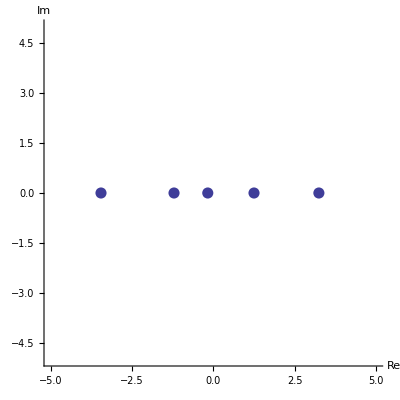

```mathematica
RootPlot[CharacteristicPolynomial[hermitianpart,x], 5]
```

Return now to ✶✶✶ and repeat (several times) the preceding sequence of commands.

This result illustrates the general circumstance which, in fact and in particular, accounts for all the real numbers that issue theoretically from quantum mechanics, and that are supposed to account fo the results of "meter readings" (measurements).

The eigenvectors of a matrix arise by solution of an equation of the form

matrix.eigenvector==number*eigenvector

which is possible iff "number" is in fact one or another of the eigenvalues of the matrix. The eigenvectors can be produced by the command

```mathematica
?Eigenvectors
```

Eigenvectors[m] gives a list of the eigenvectors of the square matrix m. 
Eigenvectors[{m,a}] gives the generalized eigenvectors of m with respect to a. 
Eigenvectors[m,k] gives the first k eigenvectors of m. 
Eigenvectors[{m,a},k] gives the first k generalized eigenvectors.

but it is usually more informative/efficient to use

```mathematica
?Eigensystem
```

Eigensystem[m] gives a list {values,vectors} of the eigenvalues and eigenvectors of the square matrix m. 
Eigensystem[{m,a}] gives the generalized eigenvalues and eigenvectors of m with respect to a. 
Eigensystem[m,k] gives the eigenvalues and eigenvectors for the first k eigenvalues of m. 
Eigensystem[{m,a},k] gives the first k generalized eigenvalues and eigenvectors.

The following simple example is designed to show how this works:

```mathematica
S=({{1, 2}, {2, 3}});
```

```mathematica
Eigensystem[S]
```

{{2+√5,2-√5},{{-3/2+1/2 (2+√5),1},{-3/2+1/2 (2-√5),1}}}

We use that information to define

```mathematica
eigenvalue1=2+√5
eigenvector1=({{-3/2+1/2 (2+√5)}, {1}})
eigenvalue2=2-√5
eigenvector2=({{-3/2+1/2 (2-√5)}, {1}})
```

2+√5

{{-3/2+1/2 (2+√5)},{1}}

2-√5

{{-3/2+1/2 (2-√5)},{1}}

and find that indeed

```mathematica
S.eigenvector1==eigenvalue1*eigenvector1
S.eigenvector2==eigenvalue2*eigenvector2
```

True

True

The evident orthogonality of the eigenvectors

```mathematica
Transpose[eigenvector1].eigenvector2//Simplify
```

{{0}}

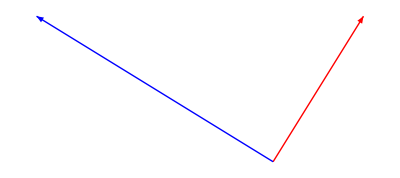

```mathematica
Show[Graphics[{
{RGBColor[1,0,0],Arrow[{{0,0},Transpose[eigenvector1]⟦1⟧}]},
{RGBColor[0,0,1],Arrow[{{0,0},Transpose[eigenvector2]⟦1⟧}]}
}],AspectRatio->Automatic]
```

can readily be shown to be follow from the real symmetry of the matrix, just as the reality of the eigenvalues does.

## Differential & Integral Calculus

For basic information concerning the calculus, in all of its many parts, as implemented in Mathematica, go to Documentation Center, search for guide/Calculus and NumericalCalculus/guide/NumericalCalculusPackage and inspect the links provided there. Here I will be able to discuss only a few of the most essential concepts.

### Simple Indefinite/Definite Integrals

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

The ≫ takes you to ref/Integrate, which provides basic information, tutorials and links to sources that treat specialized topics.

Mathematica has its own esoteric ways of doing integrals, and has also committed to memory the contents of all standard integral tables. Integrals that it can't do analytically it is always prepared to do numerically.

Integral commands can be entered in three distinct ways: in "telegraphic style" from the keyboard; with 2D symbols constructed by keyboard codes; by means of the BasicMathInput palette. I will illustrate those three methods in turn.

#### Examples of Indefinite Integrals

```mathematica
Integrate[Sech[x]^2,x]
```

Tanh[x]

That was a "telegraphic" command. We might alternatively have used the BasicMathInput palette (being very careful of its "unfortunate quirk") or typed EscinttEsc to produce

```mathematica
∫□ⅆ□
```

and then filled in the boxes to obtain

```mathematica
∫Sech[x]^2 ⅆx
```

Tanh[x]

Another indefinite integral :

```mathematica
∫1/(1+x^3)ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

REMARK: To create fractions—like, for example,

```mathematica
x/y
```

—you can either use the BasicMathInput palette (being again very careful of its "unfortunate quirk") or—much more economically—type xCtrl/y, as instructed in tutorial/EnteringTwoDimensionalInput.

#### Examples of Definite Integrals

Look next to the related definite integral which I command first in telegraphic style

```mathematica
Integrate[1/(1+x^3),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

and now in 2-dimensional style:

```mathematica
∫_0^1 1/(1+x^3)ⅆx
```

1/18 (2 √3 π+Log[64])

REMARK: To create the box to receive the lower limit, type Ctrl- (control + hypen). For the upper limit type Ctrl%.

Another definite integral:

```mathematica
∫_0^∞ 6 ⅇ^(-a x)ⅆx
```

6 If[Re[a]>0,1/a,Integrate[ⅇ^(-a x),{x,0,∞},Assumptions→Re[a]≤0]]

NOTE: Don't fail to notice the 6 that stands n front of the If.

And yet another, the Gaussian integral:

```mathematica
∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx
```

If[Re[a]>0,(√π)/(√a),Integrate[ⅇ^(-a x^2),{x,-∞,∞},Assumptions→Re[a]≤0]]

It is one of Mathematica's more CURIOUS QUIRKs that in such output statements, the Assumptions stated are those which would cause the reported result to become invalid! Compare the results of the following commands, or which the first is quoted from Mathematica's output statement, and the second has the inequality adjusted to conform to our true intent and expectation:

```mathematica
Integrate[6 ⅇ^(-a x),{x,0,∞},Assumptions->Re[a]≤0]
Integrate[6 ⅇ^(-a x),{x,0,∞},Assumptions->Re[a]>0]
```

Integrate::idiv: Integral of ⅇ^-a\ x does not converge on {0, ∞}.

Integrate[6 ⅇ^(-a x),{x,0,∞},Assumptions→Re[a]≤0]

6/a

Here I use the Gaussian integral to provide the same sort of comparison:

```mathematica
Integrate[ⅇ^(-a x^2),{x,-∞,∞},Assumptions->Re[a]≤0]
Integrate[ⅇ^(-a x^2),{x,-∞,∞},Assumptions->Re[a]>0]
```

If[Re[a]==0,((-a^2)^(3/4) √(π/2) (-1+Sign[a]))/a^2,Integrate[ⅇ^(-a x^2),{x,-∞,∞},Assumptions→Re[a]<0]]

(√π)/(√a)

### Functions Defined by Integrals

It is often the case even of integrals with simple integrands that they can be described only in terms of fancy functions (which in many case were historically defined by integrals): thus

```mathematica
∫Log[1-x^2]/x ⅆx
∫Exp[1-x^2]ⅆx
∫Sin[x^2]ⅆx
```

-1/2 PolyLog[2,x^2]

1/2 ⅇ √π Erf[x]

√(π/2) FresnelS[√(2/π) x]

But Mathematica stands ready to tell us about those higher functions: thus

```mathematica
?FresnelS
```

FresnelS[z] gives the Fresnel integral S(z).

And often we can gain a sense of what they are about by constructing a figure:

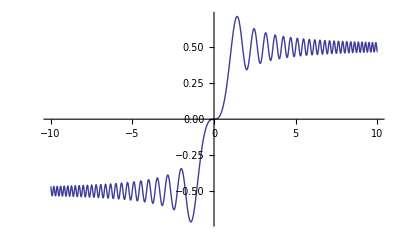

```mathematica
Plot[FresnelS[x],{x,-10,10}]
```

### Numerical Integration

But sometimes the arsenal of higher functions is inadequate to the task: some integrals are simply intractable. An example:

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

In such cases one can, however, proceed numerically

```mathematica
NIntegrate[x^x,{x,0,1}]
```

0.783431

and can even plot the results of a continuum of numerical integrations:

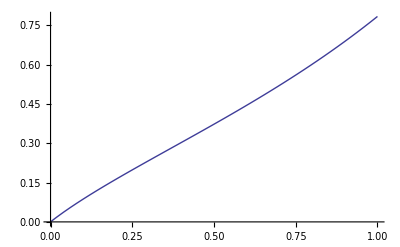

```mathematica
Plot[NIntegrate[x^x,{x,0,y}],{y,0,1}]
```

The numerical evaluation of integrals is, as we just saw, very easy to command, and Mathematica is able to deal automatically with various pathologies

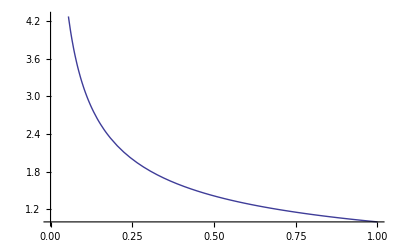

```mathematica
Plot[1/(√x), {x,0,1}]
```

```mathematica
NIntegrate[1/(√x),{x,0,1}]
```

2.

In some such cases Mathematica makes a best effort, but posts a cautionary flag:

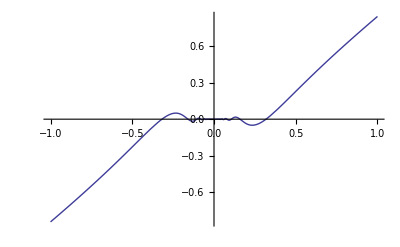

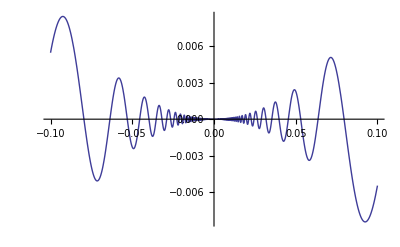

```mathematica
Plot[x^2 Sin[1/x], {x,-1,1}]
Plot[x^2 Sin[1/x], {x,-0.1,0.1}]
```

```mathematica
NIntegrate[x^2 Sin[1/x], {x,-1,1}]
NIntegrate[x^2 Sin[1/x], {x,-1,2}]
```

0.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.38755

For additional information about numerical integration, command

```mathematica
?NIntegrate
```

NIntegrate[f,{x,x_min,x_max}] gives a numerical approximation to the integral ∫_x_min^x_max f dx. 
NIntegrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives a numerical approximation to the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

follow the » and inspect the links provided at the bottom of that page.

## Ordinary & Partial Differentiation

```mathematica
?Derivative
```

f' represents the derivative of a function f of one argument. 
Derivative[n_1,n_2,…][f] is the general form, representing a function obtained from f by differentiating n_1 times with respect to the first argument, n_2 times with respect to the second argument, and so on.

The » takes you to ref/Derivative, which provides examples and useful links to tutorials and special topics.

### Ordinary Derivatives (Functions of a Single Variable)

The preferred way to command low-order differentiation of a function of a single variable is to use primes:

```mathematica
f[x_]:=x^n
```

```mathematica
f'[x]
f''[x]
f'''[x]
```

n x^(-1+n)

(-1+n) n x^(-2+n)

(-2+n) (-1+n) n x^(-3+n)

We might alternatively have commanded

```mathematica
D[f[x],x]
D[f[x],{x,2}]
D[f[x],{x,3}]
```

n x^(-1+n)

(-1+n) n x^(-2+n)

(-2+n) (-1+n) n x^(-3+n)

although…

### Partial Derivatives (Functions of Several Variables)

… D[ ] is more commonly used to construct ordinary derivatives of high order

```mathematica
D[f[x],{x,17}]
```

(-16+n) (-15+n) (-14+n) (-13+n) (-12+n) (-11+n) (-10+n) (-9+n) (-8+n) (-7+n) (-6+n) (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n x^(-17+n)

and partial derivatives:

```mathematica
g[x_,y_]:=x^n Sin[y]
```

```mathematica
D[g[x,y],x]
D[g[x,y],y]

D[g[x,y],{x,2}]
D[g[x,y],x,y]
D[g[x,y],{y,2}]
```

n x^(-1+n) Sin[y]

x^n Cos[y]

(-1+n) n x^(-2+n) Sin[y]

n x^(-1+n) Cos[y]

-x^n Sin[y]

Expressions like D[h[x,y],x,x,x,x,y,y,y,y,y,y] are—though seldom encountered—quite tedious to type. Mathematica recognized this alternative:

```mathematica
Derivative[4,6][h][x,y]=== D[h[x,y],x,x,x,x,y,y,y,y,y,y]
```

True

### Unspecified Functions

Suppose we write f[x] and g[x] to indicate that we are thinking about a couple of generic functions—functions to which we have assigned no specific meaning. Mathematica is content to work at such a level of abstraction, and is easily able to return all the standard relationships—identities—in, if you request, generalized form:

```mathematica
Clear[f,g]
```

```mathematica
D[f[x]g[x],x] (*Product Rule*)
```

g[x] f'[x]+f[x] g'[x]

```mathematica
D[f[x]g[x],{x,2}] (*Leibniz' Rule: generalized Product Rule*)
D[f[x]g[x],{x,3}]
D[f[x]g[x],{x,4}]
```

2 f'[x] g'[x]+g[x] f''[x]+f[x] g''[x]

3 g'[x] f''[x]+3 f'[x] g''[x]+g[x] f^(3)[x]+f[x] g^(3)[x]

6 f''[x] g''[x]+4 g'[x] f^(3)[x]+4 f'[x] g^(3)[x]+g[x] f^(4)[x]+f[x] g^(4)[x]

```mathematica
D[f[x]/g[x],x] (*Quotient Rule*)
```

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

```mathematica
Together[%]
```

(g[x] f'[x]-f[x] g'[x])/g[x]^2

```mathematica
D[f[g[x]],x] (*Chain Rule and higher order generalizations*)
D[f[g[x]],{x,2}] 
D[f[g[x]],{x,3}]
```

f'[g[x]] g'[x]

g'[x]^2 f''[g[x]]+f'[g[x]] g''[x]

3 g'[x] f''[g[x]] g''[x]+g'[x]^3 f^(3)[g[x]]+f'[g[x]] g^(3)[x]

NOTE the notation that Mathematica reserves for derivatives of order higher than 2.

```mathematica
D[∫_0^x f[u]ⅆu,x] (*Fundamental Theorem of the Calculus*)
∫_0^x D[f[u],u]ⅆu
```

f[x]

-f[0]+f[x]

Mathematica is comfortable also with dummy functions of several variables.  For example, we have

```mathematica
D[f[x,y]g[x,y],x,y]
D[f[x,g[x,y]],x,y]
```

g^(0,1)[x,y] f^(1,0)[x,y]+f^(0,1)[x,y] g^(1,0)[x,y]+g[x,y] f^(1,1)[x,y]+f[x,y] g^(1,1)[x,y]

g^(0,1)[x,y] f^(0,2)[x,g[x,y]] g^(1,0)[x,y]+g^(0,1)[x,y] f^(1,1)[x,g[x,y]]+f^(0,1)[x,g[x,y]] g^(1,1)[x,y]

NOTE the notation used by Mathematica to name partial derivatives.

### Implicit Differentiation

This technique is often quite useful, though it is my impression that it is no longer taught in introductory calculus courses.  I learned it from F. L. Griffin (Reed College's very first faculty member, in whose last class (Analytical Geometry, Spring 1952) I was a student), and take my example from §30 of his Mathematical Analysis Higher Course (1927).

```mathematica
Clear[x,y,a]
```

Suppose we know of y[x] only that x^2+y^2=10x y+a^2 and want to obtain y''[x]. Rather than solving for y[x]and then double differentiating, we proceed by clever indirection: we construct

```mathematica
D[x^2+y[x]^2-10x y[x]-a^2,x]
```

2 x-10 y[x]-10 x y'[x]+2 y[x] y'[x]

surely vanishes; we use this information to obtain a description of y'[x]:

```mathematica
Solve[2 x-10 y[x]-10 x y'[x]+2 y[x] y'[x]==0,y'[x]]
```

{{y'[x]→(x-5 y[x])/(5 x-y[x])}}

Define

```mathematica
firstderivative[x_]:=(x-5 y[x])/(5 x-y[x])
```

and obtain

```mathematica
D[firstderivative[x],x]
```

(1-5 y'[x])/(5 x-y[x])-((x-5 y[x]) (5-y'[x]))/(5 x-y[x])^2

Define

```mathematica
secondderivative[x_,p_]:=((-x+5 y[x]) (5-p))/(5 x-y[x])^2-(-1+5 p)/(5 x-y[x])
```

and obtain

```mathematica
secondderivative[x,firstderivative[x]]
```

-(-1+(5 (x-5 y[x]))/(5 x-y[x]))/(5 x-y[x])+((5-(x-5 y[x])/(5 x-y[x])) (-x+5 y[x]))/(5 x-y[x])^2

so0

```mathematica
Simplify[%]
```

-(24 (x^2-10 x y[x]+y[x]^2))/(5 x-y[x])^3

But it was announced at the outset that x^2+y^2-10x y=a^2 so we have finally

```mathematica
y''[x]==(24 a^2)/(y-5x)^3
```

### Maxima & Minima

The following commands serve to define a simple function and to locate its extrema:

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3-9x+5
```

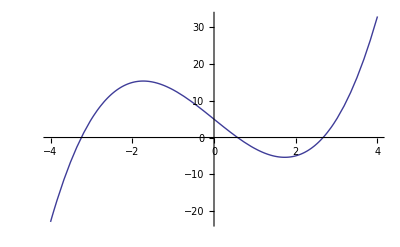

```mathematica
Plot[f[x],{x,-4,4}]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→-√3},{x→√3}}

```mathematica
N[%]
```

{{x→-1.73205},{x→1.73205}}

Those results agree with the impression conveyed by the figure.  We will decorate the figure to make the point more vivid:

```mathematica
extrema={x,f[x]}/.%
```

{{-1.73205,15.3923},{1.73205,-5.3923}}

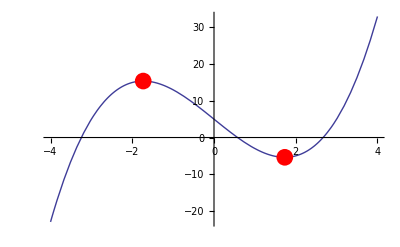

```mathematica
Plot[f[x],{x,-4,4},
Epilog->{PointSize[0.03],Hue[1],Map[Point, extrema]}]
```

I have borrowed this discussion from Torrence & Torrence (The Students' Introduction to Mathematica (1999)), page 140.  Concerning the blue details, they have this to say: The Epilog command can be used with any command that produces graphics…It allows you to overlay "graphics primitives" (such as points) on the graphic after it has been rendered. [We adjusted the pointsize and color to make them more visible.] The Map[Point, extrema] produces a list of primitive point objects, one for each point in the list we named extrema.

Concerning the ReplaceAll command /. see

```mathematica
?/.
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr.

## Limits & Series

These are distinct but closely related topics, which I have lumped  together for reasons that in Mathematica 6 have become irrelevant.  For basic information, command

```mathematica
?Limit
?Series
```

Limit[expr,x->x_0] finds the limiting value of expr when x approaches x_0.

RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", StyleBox["n", "TI"]}], "}"}]}], "]"}] generates a power series expansion for StyleBox["f", "TI"] about the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}] to order SuperscriptBox[RowBox[{"(", RowBox[{StyleBox["x", "TI"], "-", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ")"}], StyleBox["n", "TI"]]. 
RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["x", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] successively finds series expansions with respect to StyleBox["x", "TI"], then StyleBox["y", "TI"].

and consult the sites to which » leads you.

### Evaluation of Limits

#### First Example

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Sin[x]/x
```

At x = 0 we get the improper construction 0/0, yet from the figure

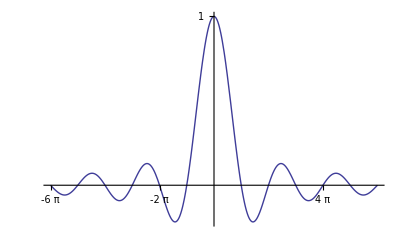

```mathematica
Plot[f[x],{x,-6π,6π}, PlotRange->All, Ticks->{{-6π,-4π,-2π,2π,4π,6π},{1}}]
```

we see that the function is perfectly well-behaved there, and are not surprised to obtain

```mathematica
Limit[f[x],x->0]
```

1

Expansion about the origin shows how this result is achieved:

```mathematica
Series[f[x], {x,0,4}]
```

1-x^2/6+x^4/120+O[x]^5

Also of interest is the statement

```mathematica
Limit[f[x],x->∞]
```

0

#### Second Example

```mathematica
Clear[g]
```

Look now to the function

```mathematica
g[x_]:=1/x
```

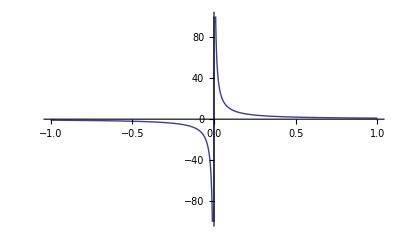

```mathematica
Plot[g[x],{x,-1,1}, PlotRange->{-100,100}]
```

```mathematica
Limit[g[x],x->0]
```

∞

Evidently Mathematica has, by default, elected to approach the origin from the right. One can reverse the direction of approach by modifying the command:

```mathematica
Limit[g[x],x->0, Direction->1]
```

-∞

#### Third Example

While the function

```mathematica
ⅇ^-x
```

has well defined asymptotic limits

```mathematica
Limit[ⅇ^-x,x->∞]
Limit[ⅇ^-x,x->-∞]
```

0

∞

the function

```mathematica
Sin[x]
```

possesses no such limits, but forever buzzes within a well-defined interval. Mathematica tells you so:

```mathematica
Limit[Sin[x],x->∞]
Limit[Sin[x],x->-∞]
```

Interval[{-1,1}]

Interval[{-1,1}]

### Construction and Summation of Power Series

These are obviously related—yet quite distinct—subjects. To discover what Mathematica has to say about them, go to Documentation Center and search for tutorial/SeriesLimitsAndResidues/Overview.

### Construction of Series

#### Examples: Some Familiar, Some Less Familiar

```mathematica
Series[Log[1+x],{x,0,10}]
Series[ArcTan[x],{x,0,10}]
Series[1/(1-x),{x,0,10}]
Series[1/(1-x)Log[1/(1-x)],{x,0,10}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+O[x]^11

x-x^3/3+x^5/5-x^7/7+x^9/9+O[x]^11

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+O[x]^11

x+(3 x^2)/2+(11 x^3)/6+(25 x^4)/12+(137 x^5)/60+(49 x^6)/20+(363 x^7)/140+(761 x^8)/280+(7129 x^9)/2520+(7381 x^10)/2520+O[x]^11

In the latter connection we note that

```mathematica
Table[Sum[1/k,{k,1,n}],{n,1,10}]
```

{1,3/2,11/6,25/12,137/60,49/20,363/140,761/280,7129/2520,7381/2520}

Just as interesting integrals are sometimes taken to define numbers/functions, so are interesting series. For example, the following series serves to define the Bernoulli numbers

```mathematica
Series[t/(ⅇ^t-1),{t,0,10}]
```

1-t/2+t^2/12-t^4/720+t^6/30240-t^8/1209600+t^10/47900160+O[t]^11

```mathematica
Table[BernoulliB[n]/(n!),{n,0,10}]
```

{1,-1/2,1/12,0,-1/720,0,1/30240,0,-1/1209600,0,1/47900160}

The series discussed above are all Maclaurin series (expansions about x = 0). Taylor series are produced by a slight variation of the same command:

```mathematica
Clear[f]
```

```mathematica
Series[f[x],{x,a,4}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+1/24 f^(4)[a] (x-a)^4+O[x-a]^5

REMARK: The command

```mathematica
Normal[%]
```

f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f^(3)[a]+1/24 (-a+x)^4 f^(4)[a]

lops off the annoying  O[ ]^n term that otherwise terminates every application of the Series command.

### Sums, and the Summation of Series

#### Examples: Some Familiar, Some Less Familiar

```mathematica
∑_(k=1)^n k
∑_(k=1)^n k^2
∑_(k=1)^n k^3
```

1/2 n (1+n)

1/6 n (1+n) (1+2 n)

1/4 n^2 (1+n)^2

Just as definite integrals very often serve to define the so-called "higher functions," so also do infinite sums:

```mathematica
∑_(n=0)^∞ 1/(n!)x^n
∑_(n=0)^∞ 1/(n!)^2 x^n
∑_(n=0)^∞ 1/((2n)!)x^n
∑_(n=0)^∞ (n!)/((2n)!)x^n
∑_(n=1)^∞ 1/n^x
```

ⅇ^x

BesselI[0,2 √x]

Cosh[√x]

1/2 (2+ⅇ^(x/4) √π √x Erf[(√x)/2])

Zeta[x]

REMARK: The keyboard command EscsumtEsc serves to create

```mathematica
∑_(□=□)^□ □
```